```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

generic model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC} initialized

classes model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA} initialized

in total: 1 Particles insertion

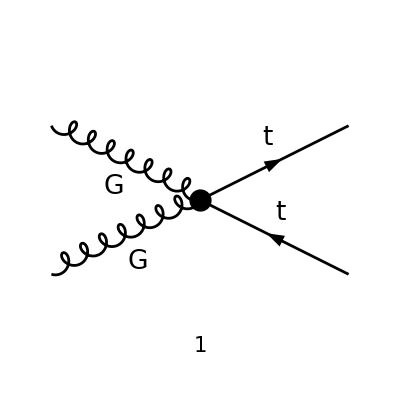

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4], V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC" ,ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9],V[4]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 1 Particles amplitude

ⅈ gs^2 π^2 yDM^2 (-C1 (γ·p1).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4-C11 (γ·p1).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4-C12 (γ·p1).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4+C1 (γ·p2).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4+C11 (γ·p2).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4+C12 (γ·p2).(γ̄)^6 g^μν (T^Glu1 T^Glu2)_Col3Col4+C11 γ^ν.(γ̄)^6 k1^μ (T^Glu1 T^Glu2)_Col3Col4-C12 γ^ν.(γ̄)^6 k1^μ (T^Glu1 T^Glu2)_Col3Col4-C1 γ^ν.(γ̄)^6 k2^μ (T^Glu1 T^Glu2)_Col3Col4+C11 γ^ν.(γ̄)^6 k2^μ (T^Glu1 T^Glu2)_Col3Col4-3 C12 γ^ν.(γ̄)^6 k2^μ (T^Glu1 T^Glu2)_Col3Col4-C1 γ^ν.(γ̄)^6 p1^μ (T^Glu1 T^Glu2)_Col3Col4-C11 γ^ν.(γ̄)^6 p1^μ (T^Glu1 T^Glu2)_Col3Col4-C12 γ^ν.(γ̄)^6 p1^μ (T^Glu1 T^Glu2)_Col3Col4+C1 γ^ν.(γ̄)^6 p2^μ (T^Glu1 T^Glu2)_Col3Col4+C11 γ^ν.(γ̄)^6 p2^μ (T^Glu1 T^Glu2)_Col3Col4+C12 γ^ν.(γ̄)^6 p2^μ (T^Glu1 T^Glu2)_Col3Col4+C1 γ^μ.(γ̄)^6 k1^ν (T^Glu1 T^Glu2)_Col3Col4-C11 γ^μ.(γ̄)^6 k1^ν (T^Glu1 T^Glu2)_Col3Col4+3 C12 γ^μ.(γ̄)^6 k1^ν (T^Glu1 T^Glu2)_Col3Col4-C11 γ^μ.(γ̄)^6 k2^ν (T^Glu1 T^Glu2)_Col3Col4+C12 γ^μ.(γ̄)^6 k2^ν (T^Glu1 T^Glu2)_Col3Col4-C1 γ^μ.(γ̄)^6 p1^ν (T^Glu1 T^Glu2)_Col3Col4-C11 γ^μ.(γ̄)^6 p1^ν (T^Glu1 T^Glu2)_Col3Col4-C12 γ^μ.(γ̄)^6 p1^ν (T^Glu1 T^Glu2)_Col3Col4+C1 γ^μ.(γ̄)^6 p2^ν (T^Glu1 T^Glu2)_Col3Col4+C11 γ^μ.(γ̄)^6 p2^ν (T^Glu1 T^Glu2)_Col3Col4+C12 γ^μ.(γ̄)^6 p2^ν (T^Glu1 T^Glu2)_Col3Col4+(C11-C12) (γ·k1).(γ̄)^6 g^μν ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)-(C11-C12) (γ·k2).(γ̄)^6 g^μν ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)+(-(C1+C11+C12) (γ·p1).(γ̄)^6 g^μν+(C1+C11+C12) (γ·p2).(γ̄)^6 g^μν-C11 γ^ν.(γ̄)^6 k1^μ+C12 γ^ν.(γ̄)^6 k1^μ+C1 γ^ν.(γ̄)^6 k2^μ-C11 γ^ν.(γ̄)^6 k2^μ+3 C12 γ^ν.(γ̄)^6 k2^μ-C1 γ^ν.(γ̄)^6 p1^μ-C11 γ^ν.(γ̄)^6 p1^μ-C12 γ^ν.(γ̄)^6 p1^μ+C1 γ^ν.(γ̄)^6 p2^μ+C11 γ^ν.(γ̄)^6 p2^μ+C12 γ^ν.(γ̄)^6 p2^μ-C1 γ^μ.(γ̄)^6 k1^ν+C11 γ^μ.(γ̄)^6 k1^ν-3 C12 γ^μ.(γ̄)^6 k1^ν+C11 γ^μ.(γ̄)^6 k2^ν-C12 γ^μ.(γ̄)^6 k2^ν-C1 γ^μ.(γ̄)^6 p1^ν-C11 γ^μ.(γ̄)^6 p1^ν-C12 γ^μ.(γ̄)^6 p1^ν+(C1+C11+C12) γ^μ.(γ̄)^6 p2^ν) (T^Glu2 T^Glu1)_Col3Col4)

```mathematica
(* Fix Gauge and replace C00ren by the PV loop integrals and the counter-term *)
ampC =ampB/.{GaugeXi[V[Index[Generic,5]]]->1};
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

```mathematica
ampEsimp=FCReplaceMomenta[ampC,{k1->p1+p2}];
```

```mathematica
ampEsimp2=FullSimplify[ExpandScalarProduct[DiracSimplify[ampEsimp/.{DiracGamma[7]->1-DiracGamma[6]}]]]
```

-ⅈ π^2 gs^2 yDM^2 ((T^Glu1 T^Glu2)_Col3Col4 ((C1+2 C12) g^μν (γ·p1).(γ̄)^6-2 (C1+2 C12) p2^ν γ^μ.(γ̄)^6-C1 g^μν (γ·p2).(γ̄)^6+C1 k2^μ γ^ν.(γ̄)^6+C1 p1^μ γ^ν.(γ̄)^6-C1 p2^μ γ^ν.(γ̄)^6+(C11-C12) g^μν (γ·k2).(γ̄)^6-2 C11 g^μν (γ·p2).(γ̄)^6-C11 k2^μ γ^ν.(γ̄)^6+C11 k2^ν γ^μ.(γ̄)^6+2 C11 p1^ν γ^μ.(γ̄)^6-2 C11 p2^μ γ^ν.(γ̄)^6+3 C12 k2^μ γ^ν.(γ̄)^6-C12 k2^ν γ^μ.(γ̄)^6+2 C12 p1^μ γ^ν.(γ̄)^6-2 C12 p1^ν γ^μ.(γ̄)^6)+(T^Glu2 T^Glu1)_Col3Col4 ((C1+2 C11) g^μν (γ·p1).(γ̄)^6-C1 g^μν (γ·p2).(γ̄)^6-C1 k2^μ γ^ν.(γ̄)^6+C1 p1^μ γ^ν.(γ̄)^6+2 C1 p1^ν γ^μ.(γ̄)^6-C1 p2^μ γ^ν.(γ̄)^6+(C12-C11) g^μν (γ·k2).(γ̄)^6+2 (C12-C11) p2^ν γ^μ.(γ̄)^6+C11 k2^μ γ^ν.(γ̄)^6-C11 k2^ν γ^μ.(γ̄)^6+2 C11 p1^μ γ^ν.(γ̄)^6-2 C12 g^μν (γ·p2).(γ̄)^6-3 C12 k2^μ γ^ν.(γ̄)^6+C12 k2^ν γ^μ.(γ̄)^6+4 C12 p1^ν γ^μ.(γ̄)^6-2 C12 p2^μ γ^ν.(γ̄)^6))

```mathematica
spinorChains=Tally[Cases[{ampEsimp2},DiracGamma[___].DiracGamma[___],All]][[All,1]]
singleGammas=Cases2[ampEsimp2,DiracGamma]
allTerms=Sort[Join[spinorChains,singleGammas]];
```

{(γ·k2).(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,γ^ν.(γ̄)^6,γ^μ.(γ̄)^6}

{(γ̄)^6,γ^μ,γ^ν,γ·k2,γ·p1,γ·p2}

### Coefficients for each term

```mathematica
Table[{allTerms[[i]],FullSimplify[Coefficient[ampEsimp2,allTerms[[i]]]]},{i,1,Length[allTerms]}]
```

((γ̄)^6 | 0
γ^μ | 0
γ^ν | 0
γ·k2 | 0
γ·p1 | 0
γ·p2 | 0
γ^μ.(γ̄)^6 | -ⅈ π^2 gs^2 yDM^2 (2 (T^Glu1 T^Glu2)_Col3Col4 ((C11-C12) p1^ν-(C1+2 C12) p2^ν)+2 (T^Glu2 T^Glu1)_Col3Col4 ((C1+2 C12) p1^ν+(C12-C11) p2^ν)+(C11-C12) k2^ν ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4))
γ^ν.(γ̄)^6 | -ⅈ π^2 gs^2 yDM^2 (k2^μ (C1-C11+3 C12) ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)+(T^Glu1 T^Glu2)_Col3Col4 ((C1+2 C12) p1^μ-(C1+2 C11) p2^μ)+(T^Glu2 T^Glu1)_Col3Col4 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ))
(γ·k2).(γ̄)^6 | -ⅈ π^2 gs^2 yDM^2 (C11-C12) g^μν ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)
(γ·p1).(γ̄)^6 | -ⅈ π^2 gs^2 yDM^2 g^μν ((C1+2 C11) (T^Glu2 T^Glu1)_Col3Col4+(C1+2 C12) (T^Glu1 T^Glu2)_Col3Col4)
(γ·p2).(γ̄)^6 | ⅈ π^2 gs^2 yDM^2 g^μν ((C1+2 C11) (T^Glu1 T^Glu2)_Col3Col4+(C1+2 C12) (T^Glu2 T^Glu1)_Col3Col4))

```mathematica
FullSimplify[SUNSimplify[Coefficient[ampEsimp2,C00ren]]]
```

0

```mathematica
FullSimplify[SUNSimplify[Coefficient[ampEsimp2,C1]]]
```

-ⅈ π^2 gs^2 yDM^2 ((T^Glu1 T^Glu2)_Col3Col4 (g^μν ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6)+γ^ν.(γ̄)^6 (k2^μ+p1^μ-p2^μ)-2 p2^ν γ^μ.(γ̄)^6)+(T^Glu2 T^Glu1)_Col3Col4 (g^μν ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6)-γ^ν.(γ̄)^6 (k2^μ-p1^μ+p2^μ)+2 p1^ν γ^μ.(γ̄)^6))

```mathematica
FullSimplify[SUNSimplify[Coefficient[ampEsimp2,C11]]]
```

ⅈ π^2 gs^2 yDM^2 ((T^Glu1 T^Glu2)_Col3Col4 (g^μν (-((γ·k2).(γ̄)^6-2 (γ·p2).(γ̄)^6))-γ^μ.(γ̄)^6 (k2^ν+2 p1^ν)+γ^ν.(γ̄)^6 (k2^μ+2 p2^μ))+(T^Glu2 T^Glu1)_Col3Col4 (g^μν ((γ·k2).(γ̄)^6-2 (γ·p1).(γ̄)^6)-γ^ν.(γ̄)^6 (k2^μ+2 p1^μ)+γ^μ.(γ̄)^6 (k2^ν+2 p2^ν)))

```mathematica
FullSimplify[SUNSimplify[Coefficient[ampEsimp2,C12]]]
```

-ⅈ π^2 gs^2 yDM^2 ((T^Glu2 T^Glu1)_Col3Col4 (g^μν ((γ·k2).(γ̄)^6-2 (γ·p2).(γ̄)^6)+γ^μ.(γ̄)^6 (k2^ν+4 p1^ν+2 p2^ν)-γ^ν.(γ̄)^6 (3 k2^μ+2 p2^μ))-(T^Glu1 T^Glu2)_Col3Col4 (g^μν ((γ·k2).(γ̄)^6-2 (γ·p1).(γ̄)^6)-γ^ν.(γ̄)^6 (3 k2^μ+2 p1^μ)+γ^μ.(γ̄)^6 (k2^ν+2 p1^ν+4 p2^ν)))